```mathematica
N[5899/7,15]
```

842.714285714286

```mathematica
prod := x y
```

```mathematica
x = 6; 
y = 7;
```

```mathematica
prod
```

42

```mathematica
Range[1.1,10]
```

{1.1,2.1,3.1,4.1,5.1,6.1,7.1,8.1,9.1}

```mathematica
Min[%]
```

1.1

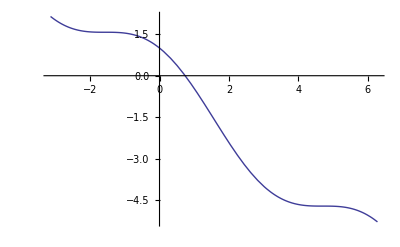

```mathematica
Plot[Cos[x]-x,{x,-Pi,2Pi}]
```

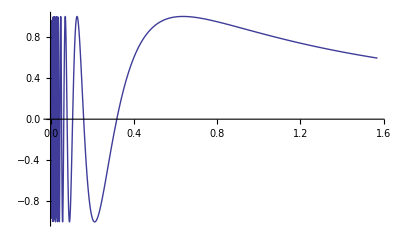

```mathematica
Plot[Sin[1/x],{x,0,Pi/2}]
```

```mathematica
FindRoot[Cos[x]-x==0,{x,0,2}]
```

{6→0.739085}

```mathematica
N[E]
```

2.71828

```mathematica
N[Pi]
```

3.14159

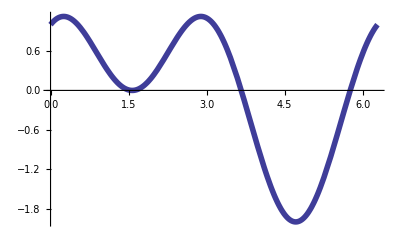

```mathematica
Plot[Sin[x]+Cos[2x],{x,0,2Pi},PlotStyle->Thickness[.01]]
```

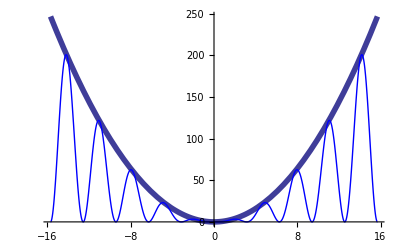

```mathematica
Plot[{x^2,x^2Sin[x]^2},{x,-5Pi,5Pi},
PlotStyle->{Thickness[.01],RGBColor[0,0,1]}]
```

```mathematica
?FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

```mathematica
??FindRoot
```

FindRoot[f,{x,x_0}] searches for a numerical root of f, starting from the point x=x_0.
FindRoot[lhs==rhs,{x,x_0}] searches for a numerical solution to the equation lhs==rhs. 
FindRoot[{f_1,f_2,…},{{x,x_0},{y,y_0},…}] searches for a simultaneous numerical root of all the f_i.
FindRoot[{eqn_1,eqn_2,…},{{x,x_0},{y,y_0},…}] searches for a numerical solution to the simultaneous equations eqn_i.

Attributes[FindRoot]={HoldAll,Protected}
 
Options[FindRoot]={AccuracyGoal→Automatic,Compiled→Automatic,DampingFactor→1,Evaluated→True,EvaluationMonitor→None,Jacobian→Automatic,MaxIterations→100,Method→Automatic,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
N[π]
```

3.14159

```mathematica
?Graphics
```

Graphics[primitives,options] represents a two-dimensional graphical image.

```mathematica
?ImplicitPlot
```

ImplicitPlot[eqn, {x, a, b}] draws a graph of the set of points that satisfy the equation eqn.  The variable x is associated with the horizontal axis and ranges from a to b.  The remaining variable in the equation is associated with the vertical axis. ImplicitPlot[eqn, {x, a, x1, x2, ..., b}] allows the user to specify values of x where special care must be exercised. ImplicitPlot[{eqn1, eqn2, ...}, {x, a, b}] allows more than one equation to be plotted, with PlotStyles set as in the Plot function. ImplicitPlot[eqn, {x, a, b}, {y, a, b}] uses a contour plot method of generating the plot.  This form does not allow specification of intermediate points.

```mathematica
ImplicitPlot[x^2+y^4==y^2-x,{x,-1.3,.3},{y,-1.2,1.2},
PlotPoints->30,AspectRatio->2.4/1.6,PlotStyle->RGBColor[0,0,1]];
```

```mathematica
x
```

6

```mathematica
y
```

7

```mathematica
f[x_]=x^2Sin[x]^2
```

36 Sin[6]^2

```mathematica
Clear[x,y]
```

```mathematica
f[x_]=x^2Sin[x]^2
```

x^2 Sin[x]^2

```mathematica
f[y]
```

y^2 Sin[y]^2

```mathematica
f[π/2]
```

π^2/4

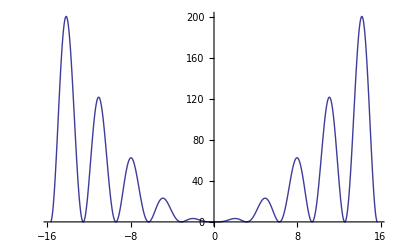

```mathematica
Plot[f[x],{x,-5Pi,5Pi}]
```

```mathematica
Clear[f]
```

```mathematica
f[x_]=Abs[x^2-4]
```

Abs[-4+x^2]

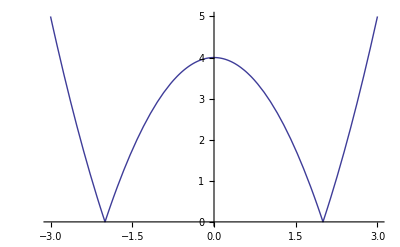

```mathematica
Plot[f[x],{x,-3,3}]
```

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
{x,{1,2},Pi}
```

{x,{1,2},π}

```mathematica
first4={1,2,3,4}
```

{1,2,3,4}

```mathematica
Table[i,{i,1,15}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

```mathematica
pts=Table[x^2,{x,1,10}]
```

{1,4,9,16,25,36,49,64,81,100}

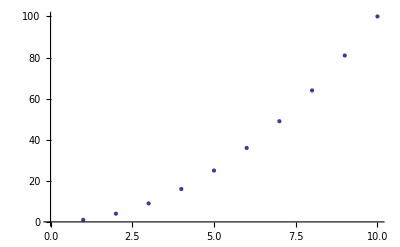

```mathematica
ListPlot[pts]
```

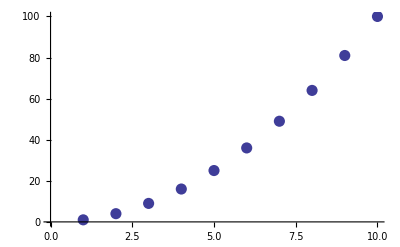

```mathematica
ListPlot[pts,PlotStyle->PointSize[.02]]
```

```mathematica
newpts=Table[{x,Sqrt[1-x^2]},{x,-1,1,.25}]
```

{{-1.,0.},{-0.75,0.661438},{-0.5,0.866025},{-0.25,0.968246},{0.,1.},{0.25,0.968246},{0.5,0.866025},{0.75,0.661438},{1.,0.}}

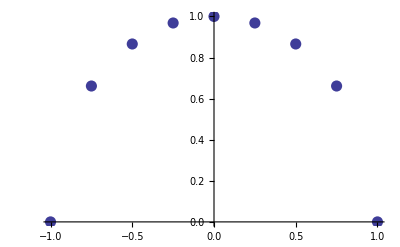

```mathematica
ListPlot[newpts,PlotStyle->PointSize[.02]]
```

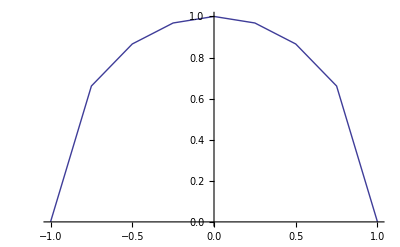

```mathematica
ListPlot[newpts,Joined->True]
```

```mathematica
pts
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
pts[[9]]
```

81

```mathematica
newpts[[2]]
```

{-0.75,0.661438}

```mathematica
newpts[[4,2]]
```

0.968246

```mathematica
newpts[[9,1]]
```

1.

```mathematica
sol=FindRoot[x^2-3==0,{x,2}]
```

{x→1.73205}

```mathematica
sol[[1]]
```

x→1.73205

```mathematica
sol[[1,1]]
```

x

```mathematica
sol[[1,2]]
```

1.73205

```mathematica
?NSolve
```

NSolve[lhs==rhs,var] gives a list of numerical approximations to the roots of a polynomial equation. 
NSolve[{eqn_1,eqn_2,…},{var_1,var_2,…}] solves a system of polynomial equations.

```mathematica
polysol=NSolve[x^4-3x^2+x==0,x]
```

{{x→-1.87939},{x→0.},{x→0.347296},{x→1.53209}}

```mathematica
polysol[[4,1,2]]
```

1.53209

```mathematica
?/.
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr.

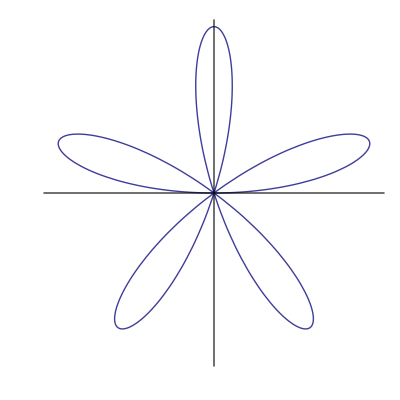

```mathematica
PolarPlot[Sin[5θ],{θ,0,π},PlotRange->{{-1,1},{-1,1}},Ticks->None]
```

```mathematica
polarframes=Table[PolarPlot[Sin[5θ],{θ,0,Subscript[θ, 0]},
			PlotRange->{{-1,1},{-1,1}},Ticks->None],
			{Subscript[θ, 0],π/12,π,π/12}];
```

```mathematica
framedisplay=Partition[polarframes,4];
```

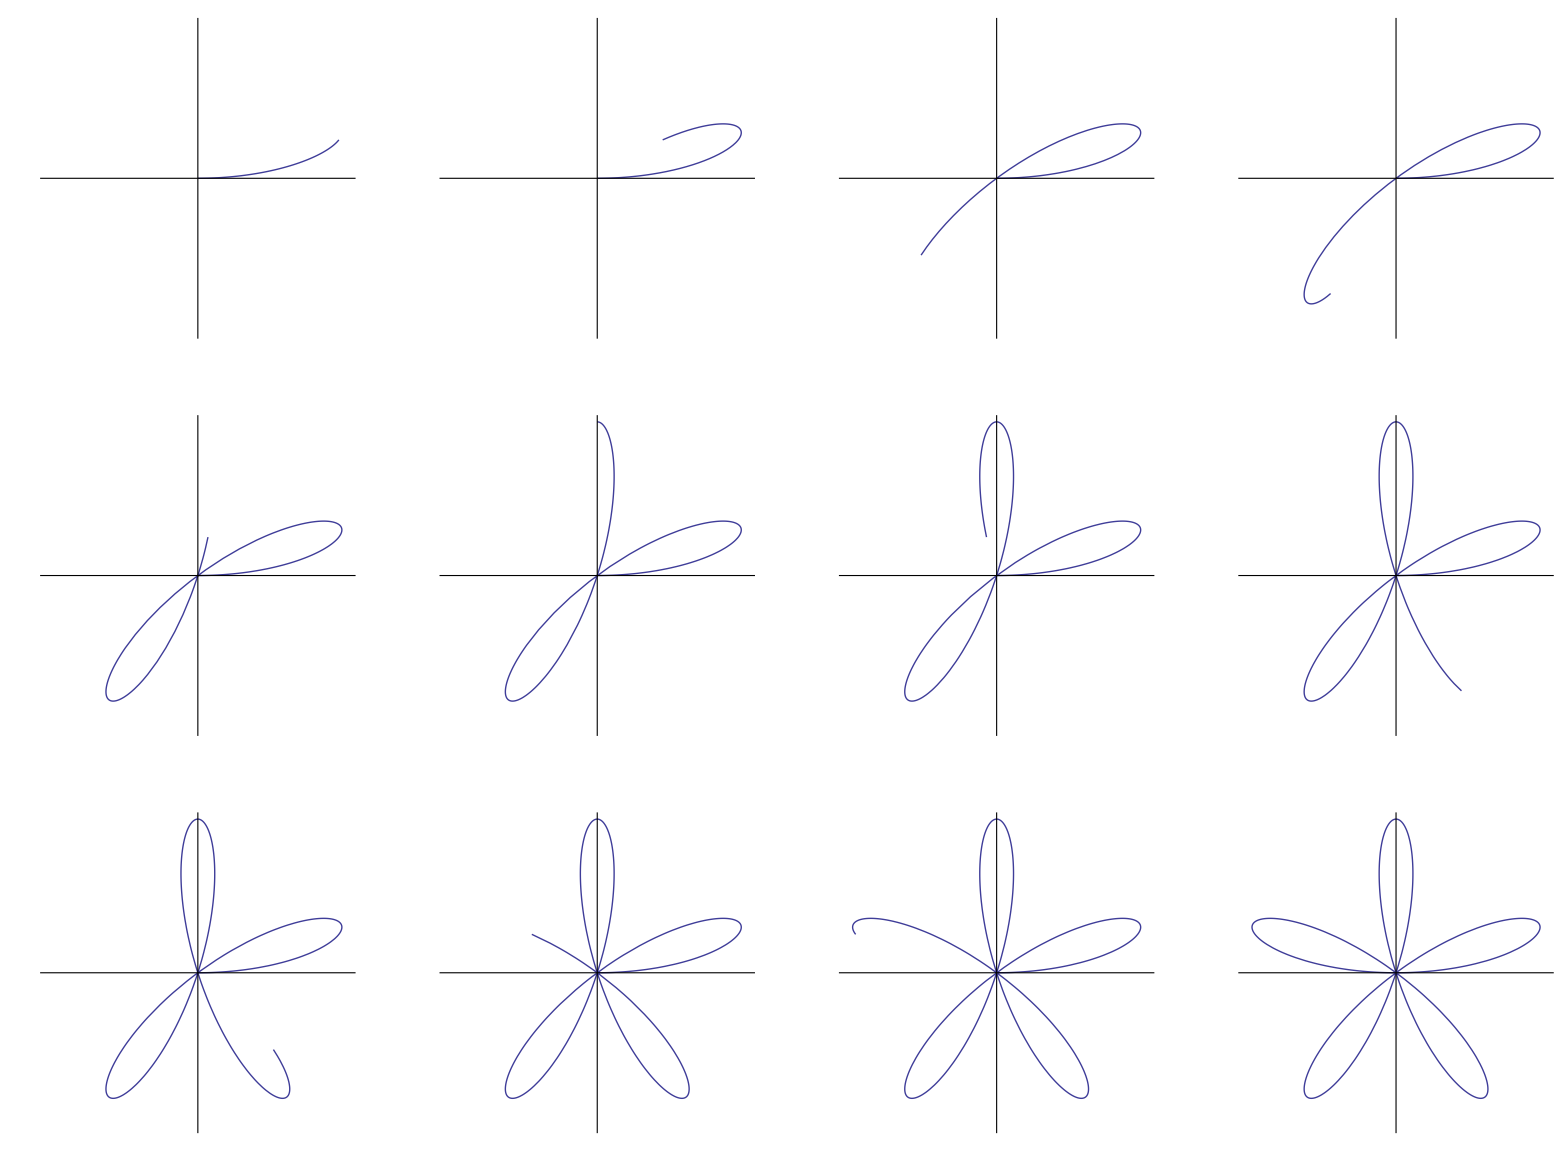

```mathematica
Show[GraphicsArray[framedisplay]]
```

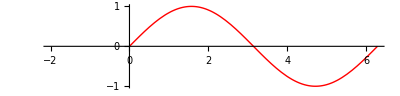

```mathematica
sinecurve=Plot[Sin[x],{x,0,2π},
PlotRange->{{-2,2π},{-1,1}},DisplayFunction->Identity,
AspectRatio->2/(2π+2),PlotStyle->RGBColor[1,0,0]]
```

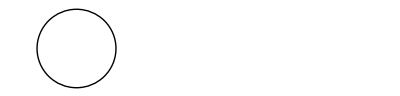

```mathematica
cir=Graphics[Circle[{-1,0},1],PlotRange->{{-2,2π},{-1,1}}]
```

```mathematica
cirptslines=Table[ListPlot[{{-1,0},{Cos[t]-1,Sin[t]},{t,Sin[t]}},
PlotRange->{{-2,2π},{-1,1}},DisplayFunction->Identity,
AspectRatio->2/(2π+2),Ticks->None,Joined->True],
{t,π/16,2π,π/16}];
```

```mathematica
movieframes=Table[Show[{cirptslines[[i]],cir,sinecurve},
DisplayFunction->$DisplayFunction],{i,1,Length[cirptslines]}];
```

```mathematica
arraydisplay=Partition[movieframes,4];
```

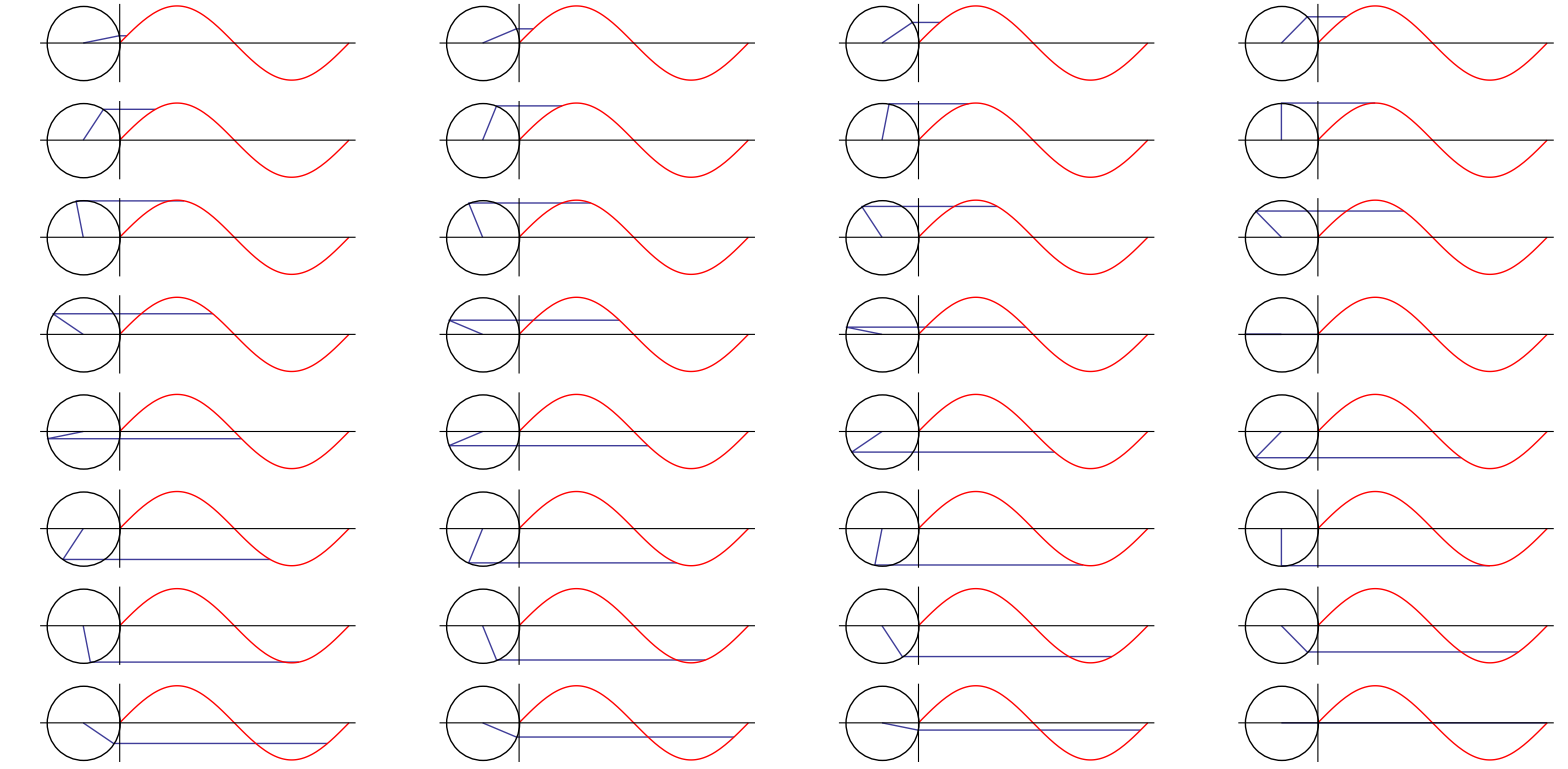

```mathematica
Show[GraphicsArray[arraydisplay]]
```

```mathematica
7(3+4)
```

49

```mathematica
mylist={π,ⅇ,1}
```

{π,ⅇ,1}

```mathematica
g[x_]=x+Sin[x];
g[π/2]
```

1+π/2

```mathematica
Cos[6π/5]
```

1/4 (-1-√5)

```mathematica
mylist[[2]]
```

ⅇ

```mathematica
??DayOfWeek
```

RowBox[{"DayOfWeek", "[", RowBox[{"{", RowBox[{StyleBox["year", "TI"], ",", StyleBox["month", "TI"], ",", StyleBox["day", "TI"]}], "}"}], "]"}] gives the day of the week on which the given date RowBox[{"{", RowBox[{StyleBox["year", "TI"], ",", StyleBox["month", "TI"], ",", StyleBox["day", "TI"]}], "}"}] occurred.
RowBox[{"DayOfWeek", "[", RowBox[{"{", RowBox[{StyleBox["year", "TI"], ",", StyleBox["month", "TI"], ",", StyleBox["day", "TI"], ",", StyleBox["hour", "TI"], ",", StyleBox["minute", "TI"], ",", StyleBox["second", "TI"]}], "}"}], "]"}] gives the day of the week for the given date.

Attributes[DayOfWeek]={Protected}
 
DayOfWeek[Calendar`Private`date_List?(Length[#1]==6&),Calendar`Private`opts___?OptionQ]:=DayOfWeek[Take[Calendar`Private`date,3],Calendar`Private`opts]
 
DayOfWeek[Calendar`Private`date_,Calendar`Private`opts___?OptionQ]/;Calendar`Private`datecheckQ[Calendar`Private`date,DayOfWeek,Calendar`Private`opts]:=With[{Calendar`Private`day=Calendar`Private`DayOfWeekNumber[Calendar`Private`date,Calendar`Private`opts]},{Sunday,Monday,Tuesday,Wednesday,Thursday,Friday,Saturday}⟦1+Calendar`Private`day⟧/;NumberQ[Calendar`Private`day]]
 
Options[DayOfWeek]:={Calendar→Automatic}

```mathematica
<<Calendar`;
```

```mathematica
DayOfWeek[{2007,6,25}]
```

Monday